```mathematica
Needs["WSMLink`"]
```

```mathematica
fieldLine =WSMSimulate["EFieldRunner",WSMParameterValues->{"tparticle1.x0"->{0,1,2,3,4},"tparticle1.y0"->{4,3,2,1,0}}]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 9.99495"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}

```mathematica
WSMPlot[fieldLine,"tparticle1.x","tparticle1.y"]
```

WSMPlot[{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]},tparticle1.x,tparticle1.y]

```mathematica
WSMPlot[{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]},"tparticle1.x","tparticle1.y"]
```

WSMPlot[{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]},tparticle1.x,tparticle1.y]

```mathematica
fieldLine =WSMSimulate["EFieldRunner",WSMParameterValues->{"tparticle1.x0"->{0,1,2,3,4},"tparticle1.y0"->{4,3,2,1,0}},{0,9.88}]
```

WSMSimulate[EFieldRunner,WSMParameterValues→{tparticle1.x0→{0,1,2,3,4},tparticle1.y0→{4,3,2,1,0}},{0,9.88}]

```mathematica
WSMPlot[fieldLine,"tparticle1.x"]
```

WSMPlot[WSMSimulate[EFieldRunner,WSMParameterValues→{tparticle1.x0→{0,1,2,3,4},tparticle1.y0→{4,3,2,1,0}},{0,9.88}],tparticle1.x]

```mathematica
fieldLine =WSMSimulate["EFieldRunner",WSMParameterValues->{"tparticle1.x0"->{0,1,2,3,4},"tparticle1.y0"->{4,3,2,1,0}}]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 7.07742"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}

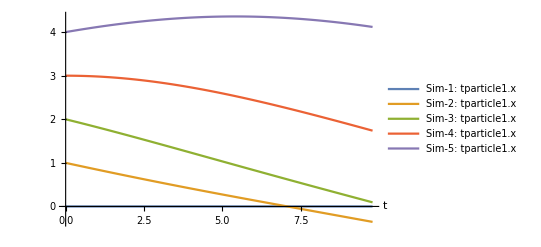

```mathematica
WSMPlot[fieldLine,"tparticle1.x"]
```

```mathematica
fieldLine =WSMSimulate["EFieldRunner",WSMParameterValues->{"tparticle1.x0"->{0,1,2,3,4},"tparticle1.y0"->{4,3,2,1,0}}]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 9.99495"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}

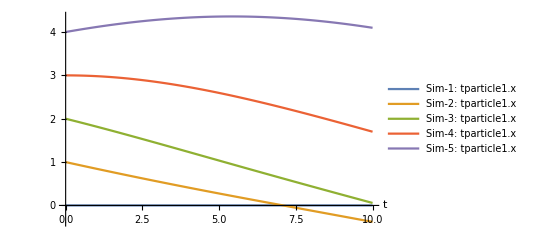

```mathematica
WSMPlot[fieldLine,"tparticle1.x"]
```

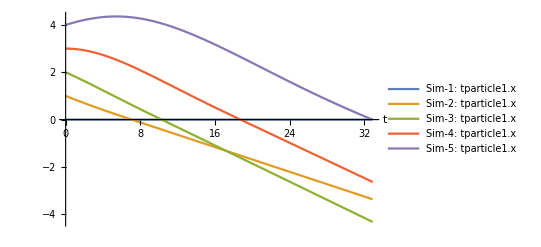

```mathematica
WSMPlot[fieldLine,"tparticle1.x",{0,32.9}]
```

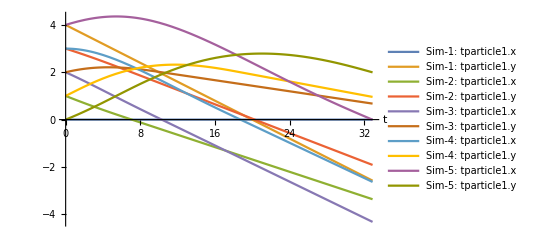

```mathematica
WSMPlot[fieldLine,{"tparticle1.x","tparticle1.y"},{0,32.9}]
```

```mathematica
x=fieldLine[{"tparticle1.x"}]
```

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}[{tparticle1.x}]

```mathematica
y=fieldLine[{"tparticle1.y"}]
```

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}[{tparticle1.y}]

```mathematica
fieldLine["VariableNames"]
```

```mathematica
{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}["VariableNames"]
```

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}[VariableNames]

```mathematica
y
```

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}[{tparticle1.y}]

```mathematica
ParametricPlot[{x,y},{t,0,32.9}]
```

-Graphics-

```mathematica
x
```

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}[{tparticle1.x}]